# Running in Circles

## 26 May 2009

Christoph Maier

### Initialization

```mathematica
Off[General::spell,General::spell1]
```

```mathematica
LSolve=Last[Solve[##]]&
```

Last[Solve[##1]]&

```mathematica
PeS=PowerExpand[Simplify[#]]&
FpPeS=FixedPoint[PeS,#]&
```

PowerExpand[Simplify[#1]]&

FixedPoint[PeS,#1]&

```mathematica
unitsquare=Function[p,Line[p+#/2&/@{{1,1},{-1,1},{-1,-1},{1,-1},{1,1}}]]
```

Function[p,Line[(p+#1/2&)/@{{1,1},{-1,1},{-1,-1},{1,-1},{1,1}}]]

## Basic algorithm

### Defining equation for a circle

x is a vector, r is the radius (well, a sphere in an Length[x]-dimensional vector space, actually)

```mathematica
circleeqn=Function[{x,r},x.x-r^2==0]
```

Function[{x,r},x.x-r^2==0]

```mathematica
circleeqn[{x,y},R]
```

-R^2+x^2+y^2==0

### Iterations

```mathematica
circleeqn[{x+1,y},R]
```

-R^2+(1+x)^2+y^2==0

```mathematica
circleeqn[#,R]⟦1⟧&/@{{x+1,y},{x,y}}
Simplify[Subtract@@%]
```

{-R^2+(1+x)^2+y^2,-R^2+x^2+y^2}

1+2 x

```mathematica
Simplify[Subtract@@(circleeqn[#,R]⟦1⟧&/@#)]&/@{{{x+1,y},{x,y}},{{x,y-1},{x,y}},{{x+1,y-1},{x,y}}}
```

{1+2 x,1-2 y,2 (1+x-y)}

### Slope

```mathematica
circleeqn[{x,y[x]},R]
D[%,x]
LSolve[%,y'[x]]
```

-R^2+x^2+y[x]^2==0

2 x+2 y[x] y'[x]==0

{y'[x]→-x/y[x]}

### Different iteration step strategies

We can define a drawing algorithm such that the only possible directions are either horizontal or vertical. In this case, we need to split a full circle into 4 quadrants. 
The discrimination criteria between quadrants are the signs of the coordinates: {+,+},{-,+},{-,-},{+,-}.

Alternatively, we can define a drawing algorithm such that the possible directions are horizontal, vertical, or diagonal. In this case, we need to split a full circle into 8 octants. 
The discrimination criteria between octants are the signs of the coordinates and the relative magnitude of the partial derivatives of the discriminating function with respect to the coordnates:
{+,+,|(∂Δ)/(∂x)|<|(∂Δ)/(∂y)|},{+,+,|(∂Δ)/(∂x)|>|(∂Δ)/(∂y)|},{-,+,|(∂Δ)/(∂x)|>|(∂Δ)/(∂y)|},{-,+,|(∂Δ)/(∂x)|<|(∂Δ)/(∂y)|},{-,-,|(∂Δ)/(∂x)|<|(∂Δ)/(∂y)|},{-,-,|(∂Δ)/(∂x)|>|(∂Δ)/(∂y)|},{+,-,|(∂Δ)/(∂x)|>|(∂Δ)/(∂y)|},{+,-,|(∂Δ)/(∂x)|<|(∂Δ)/(∂y)|}

### Orthogonal—only iteration

Assumption: We iterate in mathematically positive sense of orientation.

Quadrant | δx | δy
{+,+} | - | +
{-,+} | - | -
{-,-} | + | -
{+,-} | + | +

Underlying general rules: 
Sign[δx]=-Sign[y]; Sign[δy]= Sign[x].

We want to choose the alternative that minimizes the error, i.e., gives us min{|Δ+1+2 x δx|,|Δ+1+2 y δy|}

```mathematica
OrthogonalIterate=Function[{x,Δ},Block[{δx1=If[x⟦2⟧<0,1,-1],δx2=If[x⟦1⟧<0,-1,1],Δx,Δy},Δx1=1+2x⟦1⟧δx1;Δx2=1+2x⟦2⟧δx2;
If[Abs[Δ+Δx1] <Abs[Δ+Δx2],{x+{δx1,0},Δ+Δx1},{x+{0,δx2},Δ+Δx2}]]
]
```

Function[{x,Δ},Block[{δx1=If[x⟦2⟧<0,1,-1],δx2=If[x⟦1⟧<0,-1,1],Δx,Δy},Δx1=1+2 x⟦1⟧ δx1;Δx2=1+2 x⟦2⟧ δx2;If[Abs[Δ+Δx1]<Abs[Δ+Δx2],{x+{δx1,0},Δ+Δx1},{x+{0,δx2},Δ+Δx2}]]]

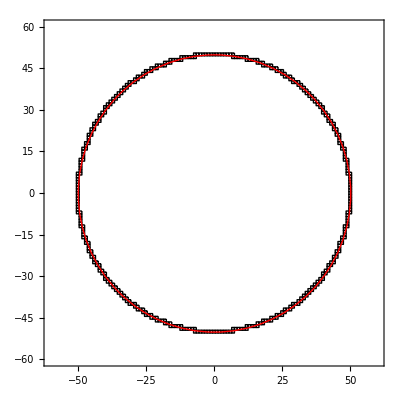

```mathematica
NestList[OrthogonalIterate@@#&,{{50,0},0},399];
Show[
Graphics[unitsquare[First[#]]&/@%,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}],Graphics[{Hue[0],Circle[{0,0},50]},Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}]]
```

### Diagonal iteration

Assumption: We iterate in mathematically positive sense of orientation.

Octant | Straight | Diagonal
{+,+,|(∂Δ)/(∂x)|>|(∂Δ)/(∂y)|} | {0,++y} | {--x,++y}
{+,+,|(∂Δ)/(∂x)|<|(∂Δ)/(∂y)|} | {--x,0} | {--x,++y}
{-,+,|(∂Δ)/(∂x)|<|(∂Δ)/(∂y)|} | {--x,0} | {--x,--y}
{-,+,|(∂Δ)/(∂x)|>|(∂Δ)/(∂y)|} | {0,--y} | {--x,--y}
{-,-,|(∂Δ)/(∂x)|>|(∂Δ)/(∂y)|} | {0,--y} | {++x,--y}
{-,-,|(∂Δ)/(∂x)|<|(∂Δ)/(∂y)|} | {++x,0} | {++x,--y}
{+,-,|(∂Δ)/(∂x)|<|(∂Δ)/(∂y)|} | {++x,0} | {++x,++y}
{+,-,|(∂Δ)/(∂x)|>|(∂Δ)/(∂y)|} | {0,++y} | {++x,++y}

Underlying general rules:
Sign[δx]=-Sign[y]; Sign[δy]= Sign[x],
straight direction is the direction of the smaller partial derivative.

We want to choose the alternative that minimizes the error.

```mathematica
DiagonalIterate=Function[{x,Δ},Block[{δx1=If[x⟦2⟧<0,1,-1],δx2=If[x⟦1⟧<0,-1,1],Δx1,Δx2,δs,Δs},Δx1=1+2x⟦1⟧δx1;Δx2=1+2x⟦2⟧δx2;
{δs,Δs}=If[Abs[x⟦1⟧]<Abs[x⟦2⟧],{{δx1,0},Δx1},{{0,δx2},Δx2}];
If[Abs[Δ+Δs]<Abs[Δ+Δx1+Δx2],
{x+δs,Δ+Δs},{x+{δx1,δx2},Δ+Δx1+Δx2}]
]
]
```

Function[{x,Δ},Block[{δx1=If[x⟦2⟧<0,1,-1],δx2=If[x⟦1⟧<0,-1,1],Δx1,Δx2,δs,Δs},Δx1=1+2 x⟦1⟧ δx1;Δx2=1+2 x⟦2⟧ δx2;{δs,Δs}=If[Abs[x⟦1⟧]<Abs[x⟦2⟧],{{δx1,0},Δx1},{{0,δx2},Δx2}];If[Abs[Δ+Δs]<Abs[Δ+Δx1+Δx2],{x+δs,Δ+Δs},{x+{δx1,δx2},Δ+Δx1+Δx2}]]]

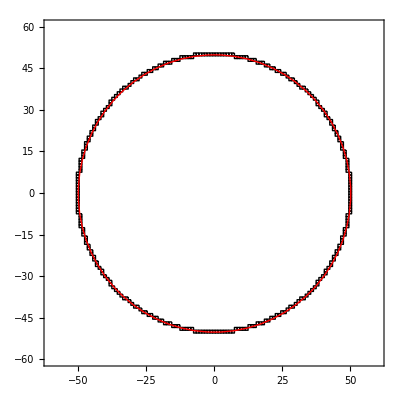

```mathematica
NestList[DiagonalIterate@@#&,{{50,0},0},283];
Show[
Graphics[unitsquare[First[#]]&/@%,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}],Graphics[{Hue[0],Circle[{0,0},50]},Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}]]
```

## Generalization to ellipses

### Basic equation

An ellipse with major and minor axes parallel to the coordinate axes has the equation x^2/a^2+y^2/b^2-1==0.

An ellipse with major axis in the direction (ξ
υ) has the equation (⟨ x | y| ξ | υ ⟩⟨ ξ | υ| x | y ⟩)/(a^2⟨ ξ | υ| ξ | υ ⟩)+(⟨ x | y| -υ | ξ ⟩⟨ -υ | ξ| x | y ⟩)/(b^2⟨ ξ | υ| ξ | υ ⟩)-1==0.

```mathematica
({ξ,υ}.{x,y})^2/(a^2({ξ,υ}.{ξ,υ}))+({-υ,ξ}.{x,y})^2/(b^2({ξ,υ}.{ξ,υ}))-1==0
Simplify[%]
```

-1+(y ξ-x υ)^2/(b^2 (ξ^2+υ^2))+(x ξ+y υ)^2/(a^2 (ξ^2+υ^2))==0

(a^2 (y ξ-x υ)^2+b^2 (x ξ+y υ)^2)/(a^2 b^2 (ξ^2+υ^2))==1

### Equation in matrix form

```mathematica
MatrixForm/@{{x,y},{{ξ,-υ},{υ,ξ}},{{1/a^2,0},{0,1/b^2}}/({ξ,υ}.{ξ,υ}),{{ξ,υ},{-υ,ξ}},{x,y}}
```

{(x
y),(ξ | -υ
υ | ξ),(1/(a^2 (ξ^2+υ^2)) | 0
0 | 1/(b^2 (ξ^2+υ^2))),(ξ | υ
-υ | ξ),(x
y)}

```mathematica
Simplify[{x,y}.{{ξ,-υ},{υ,ξ}}.({{1/a^2,0},{0,1/b^2}}/({ξ,υ}.{ξ,υ})).{{ξ,υ},{-υ,ξ}}.{x,y}==1]
```

(a^2 (y ξ-x υ)^2+b^2 (x ξ+y υ)^2)/(a^2 b^2 (ξ^2+υ^2))==1

The matrices that do not depend on the point coordinates (x
y) can be collected into one matrix:

```mathematica
MatrixForm[Simplify[{{ξ,-υ},{υ,ξ}}.({{1/a^2,0},{0,1/b^2}}/({ξ,υ}.{ξ,υ})).{{ξ,υ},{-υ,ξ}}]]
```

((b^2 ξ^2+a^2 υ^2)/(a^2 b^2 (ξ^2+υ^2)) | ((-a^2+b^2) ξ υ)/(a^2 b^2 (ξ^2+υ^2))
((-a^2+b^2) ξ υ)/(a^2 b^2 (ξ^2+υ^2)) | (a^2 ξ^2+b^2 υ^2)/(a^2 b^2 (ξ^2+υ^2)))

```mathematica
Collect[{x,y}.{{A,C},{C,B}}.{x,y},{x,y}]
```

A x^2+2 C x y+B y^2

If we want to avoid all divisions, the equation is

```mathematica
(ellipsediscriminant=Collect[{x,y}.{{ξ,-υ},{υ,ξ}}.{{b^2,0},{0,a^2}}.{{ξ,υ},{-υ,ξ}}.{x,y}-a^2 b^2{ξ,υ}.{ξ,υ},{x,y},Simplify])==0
```

2 (-a^2+b^2) x y ξ υ-a^2 b^2 (ξ^2+υ^2)+x^2 (b^2 ξ^2+a^2 υ^2)+y^2 (a^2 ξ^2+b^2 υ^2)==0

```mathematica
ellipsediscriminant
```

2 (-a^2+b^2) x y ξ υ-a^2 b^2 (ξ^2+υ^2)+x^2 (b^2 ξ^2+a^2 υ^2)+y^2 (a^2 ξ^2+b^2 υ^2)

```mathematica
LSolve[D[0==ellipsediscriminant/.y->y[x],x],y'[x]]/.y[x]->y
```

{y'[x]→(-b^2 x ξ^2+a^2 y ξ υ-b^2 y ξ υ-a^2 x υ^2)/(a^2 y ξ^2-a^2 x ξ υ+b^2 x ξ υ+b^2 y υ^2)}

```mathematica
Collect[D[ellipsediscriminant,#],{x,y},Simplify]&/@{x,y}
```

{2 (-a^2+b^2) y ξ υ+2 x (b^2 ξ^2+a^2 υ^2),2 (-a^2+b^2) x ξ υ+2 y (a^2 ξ^2+b^2 υ^2)}

### Constant coefficients that can be calculated in advance

```mathematica
Append[Limit[ellipsediscriminant/z/.{{x^2->z,y^2->0,x y->0},{x^2->0,y^2->z,x y->0},{x^2->0,y^2->0,x y->z}},z->∞],-ellipsediscriminant/.{x^2->0,y^2->0,x y->0}]
MapThread[Rule,{%,{A,B,2C,D}}]
ellipsediscriminant/.%
D[%,#]&/@{x,y}
```

{b^2 ξ^2+a^2 υ^2,a^2 ξ^2+b^2 υ^2,2 (-a^2+b^2) ξ υ,a^2 b^2 (ξ^2+υ^2)}

{b^2 ξ^2+a^2 υ^2→A,a^2 ξ^2+b^2 υ^2→B,2 (-a^2+b^2) ξ υ→2 C,a^2 b^2 (ξ^2+υ^2)→D}

-D+A x^2+2 C x y+B y^2

{2 A x+2 C y,2 C x+2 B y}

### Iterated variables

The discriminant and its gradient need not be computed from scratch for each new point, but can be iterated, exploiting the fact that for continuous lines, each of the coordinate can only change by 0 or ±1.

#### Discriminant

```mathematica
A x^2+2 C x y+B y^2-D
TableForm[%/.{{x->x+1},{x->x+1,y->y+1},{y->y+1},{x->x-1,y->y+1},{x->x-1},{x->x-1,y->y-1},{y->y-1},{x->x+1,y->y-1}}]
TableForm[Collect[#,{x,y},Simplify]&/@(%-%%)]
TableForm[Simplify[{-1,1,-1}.%⟦#⟧]&/@{{1,2,3},{3,4,5},{5,6,7},{7,8,1}}]
```

-D+A x^2+2 C x y+B y^2

-D+A (1+x)^2+2 C (1+x) y+B y^2
-D+A (1+x)^2+2 C (1+x) (1+y)+B (1+y)^2
-D+A x^2+2 C x (1+y)+B (1+y)^2
-D+A (-1+x)^2+2 C (-1+x) (1+y)+B (1+y)^2
-D+A (-1+x)^2+2 C (-1+x) y+B y^2
-D+A (-1+x)^2+2 C (-1+x) (-1+y)+B (-1+y)^2
-D+A x^2+2 C x (-1+y)+B (-1+y)^2
-D+A (1+x)^2+2 C (1+x) (-1+y)+B (-1+y)^2

A+2 A x+2 C y
A+B+2 C+2 (A+C) x+2 (B+C) y
B+2 C x+2 B y
A+B-2 C+(-2 A+2 C) x+2 (B-C) y
A-2 A x-2 C y
A+B+2 C-2 (A+C) x-2 (B+C) y
B-2 C x-2 B y
A+B-2 C+2 (A-C) x+(-2 B+2 C) y

2 C
-2 C
2 C
-2 C

#### Partial derivative of discriminant w.r.t. x

```mathematica
2(A x+C y)
TableForm[%/.{{x->x+1},{x->x+1,y->y+1},{y->y+1},{x->x-1,y->y+1},{x->x-1},{x->x-1,y->y-1},{y->y-1},{x->x+1,y->y-1}}]
TableForm[Simplify[%-%%]]
```

2 (A x+C y)

2 (A (1+x)+C y)
2 (A (1+x)+C (1+y))
2 (A x+C (1+y))
2 (A (-1+x)+C (1+y))
2 (A (-1+x)+C y)
2 (A (-1+x)+C (-1+y))
2 (A x+C (-1+y))
2 (A (1+x)+C (-1+y))

2 A
2 (A+C)
2 C
-2 A+2 C
-2 A
-2 (A+C)
-2 C
2 (A-C)

#### Partial derivative of discriminant w.r.t. y

```mathematica
2(C x+B y)
TableForm[%/.{{x->x+1},{x->x+1,y->y+1},{y->y+1},{x->x-1,y->y+1},{x->x-1},{x->x-1,y->y-1},{y->y-1},{x->x+1,y->y-1}}]
TableForm[Simplify[%-%%]]
```

2 (C x+B y)

2 (C (1+x)+B y)
2 (C (1+x)+B (1+y))
2 (C x+B (1+y))
2 (C (-1+x)+B (1+y))
2 (C (-1+x)+B y)
2 (C (-1+x)+B (-1+y))
2 (C x+B (-1+y))
2 (C (1+x)+B (-1+y))

2 C
2 (B+C)
2 B
2 (B-C)
-2 C
-2 (B+C)
-2 B
2 (-B+C)

#### Gradient of discriminant

```mathematica
2{A x+C y,C x+B y}
Outer[ReplaceAll,%,{{x->x+1},{x->x+1,y->y+1},{y->y+1},{x->x-1,y->y+1},{x->x-1},{x->x-1,y->y-1},{y->y-1},{x->x+1,y->y-1}},1];
TableForm[Transpose[%],TableDepth->1]
TableForm[Transpose[Simplify[%%-%%%]],TableDepth->1]
TableForm[Simplify[{-1,1,-1}.%⟦#⟧]&/@{{1,2,3},{3,4,5},{5,6,7},{7,8,1}},TableDepth->1]
```

{2 (A x+C y),2 (C x+B y)}

{2 (A (1+x)+C y),2 (C (1+x)+B y)}
{2 (A (1+x)+C (1+y)),2 (C (1+x)+B (1+y))}
{2 (A x+C (1+y)),2 (C x+B (1+y))}
{2 (A (-1+x)+C (1+y)),2 (C (-1+x)+B (1+y))}
{2 (A (-1+x)+C y),2 (C (-1+x)+B y)}
{2 (A (-1+x)+C (-1+y)),2 (C (-1+x)+B (-1+y))}
{2 (A x+C (-1+y)),2 (C x+B (-1+y))}
{2 (A (1+x)+C (-1+y)),2 (C (1+x)+B (-1+y))}

{2 A,2 C}
{2 (A+C),2 (B+C)}
{2 C,2 B}
{-2 A+2 C,2 (B-C)}
{-2 A,-2 C}
{-2 (A+C),-2 (B+C)}
{-2 C,-2 B}
{2 (A-C),2 (-B+C)}

{0,0}
{0,0}
{0,0}
{0,0}

### Setting up initial conditions for the iterations

```mathematica
ellipsefunction=Function[{x,Ξ,ab},
Block[{A=ab⟦2⟧^2 Ξ⟦1⟧^2+ab⟦1⟧^2 Ξ⟦2⟧^2,B=ab⟦1⟧^2 Ξ⟦1⟧^2+ab⟦2⟧^2 Ξ⟦2⟧^2,C=(ab⟦2⟧^2-ab⟦1⟧^2)Ξ⟦1⟧Ξ⟦2⟧,Δ,dΔ},{x,{Δ=A x⟦1⟧^2+B x⟦2⟧^2+2C x⟦1⟧x⟦2⟧-(ab⟦1⟧ab⟦2⟧)^2(Ξ⟦1⟧^2+Ξ⟦2⟧^2),dΔ=2{A x⟦1⟧+C x⟦2⟧,C x⟦1⟧+B x⟦2⟧}},{A,B,C}}
]
]
```

Function[{x,Ξ,ab},Block[{A=ab⟦2⟧^2 Ξ⟦1⟧^2+ab⟦1⟧^2 Ξ⟦2⟧^2,B=ab⟦1⟧^2 Ξ⟦1⟧^2+ab⟦2⟧^2 Ξ⟦2⟧^2,C=(ab⟦2⟧^2-ab⟦1⟧^2) Ξ⟦1⟧ Ξ⟦2⟧,Δ,dΔ},{x,{Δ=A x⟦1⟧^2+B x⟦2⟧^2+2 C x⟦1⟧ x⟦2⟧-(ab⟦1⟧ ab⟦2⟧)^2 (Ξ⟦1⟧^2+Ξ⟦2⟧^2),dΔ=2 {A x⟦1⟧+C x⟦2⟧,C x⟦1⟧+B x⟦2⟧}},{A,B,C}}]]

```mathematica
ellipsefunction[{x,y},{ξ,υ},{a,b}]
```

{{x,y},{2 (-a^2+b^2) x y ξ υ-a^2 b^2 (ξ^2+υ^2)+x^2 (b^2 ξ^2+a^2 υ^2)+y^2 (a^2 ξ^2+b^2 υ^2),{2 ((-a^2+b^2) y ξ υ+x (b^2 ξ^2+a^2 υ^2)),2 ((-a^2+b^2) x ξ υ+y (a^2 ξ^2+b^2 υ^2))}},{b^2 ξ^2+a^2 υ^2,a^2 ξ^2+b^2 υ^2,(-a^2+b^2) ξ υ}}

### Identifying quadrants and octants

While the identification of quadrants and octants in the case of a circle is straightforward, the proper directions of movement from one pixel to the next is not quite as obvious for a general ellipse.
The directions are determined by the sign of the partial derivative of the discriminant with respect to the coordinates, (∂Δ)/(∂x) and (∂Δ)/(∂y).

### Orthogonal—only iteration

Assumption: We iterate in mathematically positive sense of orientation (counterclockwise)

Quadrants:
(∂Δ)/(∂x) | (∂Δ)/(∂y) | δx | δy
>0 | >0 | - | +
<0 | >0 | - | -
<0 | <0 | + | -
>0 | <0 | + | +

Underlying general rules:
δx=-Sign[(∂Δ)/(∂y)], δy=Sign[(∂Δ)/(∂x)]

### Diagonal iteration

Assumption: We iterate in mathematically positive sense of orientation (counterclockwise)

Octants:
(∂Δ)/(∂x) | (∂Δ)/(∂y) | |(∂Δ)/(∂x)|-|(∂Δ)/(∂y)| | Straight | Diagonal
>0 | >0 | >0 | {0,+1} | {-1,+1}
>0 | >0 | <0 | {-1,0} | {-1,+1}
<0 | >0 | <0 | {-1,0} | {-1,-1}
<0 | >0 | >0 | {0,-1} | {-1,-1}
<0 | <0 | >0 | {0,-1} | {+1,-1}
<0 | <0 | <0 | {+1,0} | {+1,-1}
>0 | <0 | <0 | {+1,0} | {+1,+1}
>0 | <0 | >0 | {0,+1} | {+1,+1}

Underlying general rules:
δx=-Sign[(∂Δ)/(∂y)], δy=Sign[(∂Δ)/(∂x)], the straight direction is the direction for which the change in Δ is smaller.

```mathematica
EllipseDiagonalIteration=Function[{x,iterationvariables,iterationconstants},Block[{
Δ=iterationvariables⟦1⟧,
dΔ=iterationvariables⟦2⟧,
A=iterationconstants⟦1⟧,
B=iterationconstants⟦2⟧,
C=iterationconstants⟦3⟧,
δx1,δx2,Δx1,Δx2,δd1,δd2,δs,Δs,δds
},
δx1=If[dΔ⟦2⟧<0,1,-1];δx2=If[dΔ⟦1⟧<0,-1,1];
Δx1=δx1 dΔ⟦1⟧;Δx2=δx2 dΔ⟦2⟧;
δd1=2δx1{A,C};δd2=2δx2{C,B};
{δs,Δs,δds}=If[Subtract@@(Abs[dΔ])<0,
{{δx1,0},A+Δx1,δd1},{{0,δx2},B+Δx2,δd2}];
If[Abs[Δ+Δs]<Abs[Δ+A+B+2Sign[δx1]Sign[δx2]C+Δx1+Δx2],
{x+δs,{Δ+Δs,dΔ+δds},iterationconstants},
{x+{δx1,δx2},{Δ+A+B+2Sign[δx1]Sign[δx2]C+Δx1+Δx2,dΔ+δd1+δd2},iterationconstants}]
]
]
```

Function[{x,iterationvariables,iterationconstants},Block[{Δ=iterationvariables⟦1⟧,dΔ=iterationvariables⟦2⟧,A=iterationconstants⟦1⟧,B=iterationconstants⟦2⟧,C=iterationconstants⟦3⟧,δx1,δx2,Δx1,Δx2,δd1,δd2,δs,Δs,δds},δx1=If[dΔ⟦2⟧<0,1,-1];δx2=If[dΔ⟦1⟧<0,-1,1];Δx1=δx1 dΔ⟦1⟧;Δx2=δx2 dΔ⟦2⟧;δd1=2 δx1 {A,C};δd2=2 δx2 {C,B};{δs,Δs,δds}=If[Subtract@@Abs[dΔ]<0,{{δx1,0},A+Δx1,δd1},{{0,δx2},B+Δx2,δd2}];If[Abs[Δ+Δs]<Abs[Δ+A+B+2 Sign[δx1] Sign[δx2] C+Δx1+Δx2],{x+δs,{Δ+Δs,dΔ+δds},iterationconstants},{x+{δx1,δx2},{Δ+A+B+2 Sign[δx1] Sign[δx2] C+Δx1+Δx2,dΔ+δd1+δd2},iterationconstants}]]]

```mathematica
ellipsefunction[{30,0},{1,0},{30,40}]
```

{{30,0},{0,{96000,0}},{1600,900,0}}

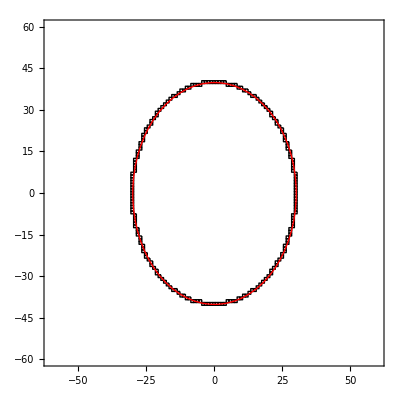

```mathematica
NestList[EllipseDiagonalIteration@@#&,ellipsefunction[{30,0},{1,0},{30,40}],199];
Show[Graphics[unitsquare[First[#]]&/@%,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}],Graphics[{Hue[0],Circle[{0,0},{30,40}]},Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}],DisplayFunction->$DisplayFunction]
```

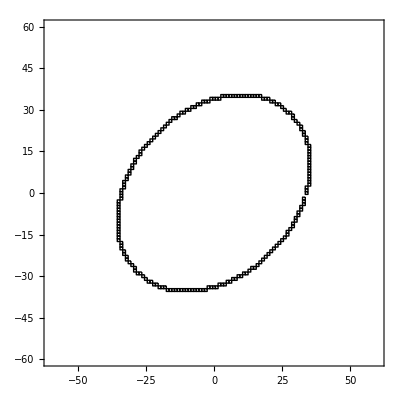

```mathematica
NestList[EllipseDiagonalIteration@@#&,ellipsefunction[{34,0},{1,1},{40,30}],196];
Show[Graphics[unitsquare[First[#]]&/@%,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}]]
```

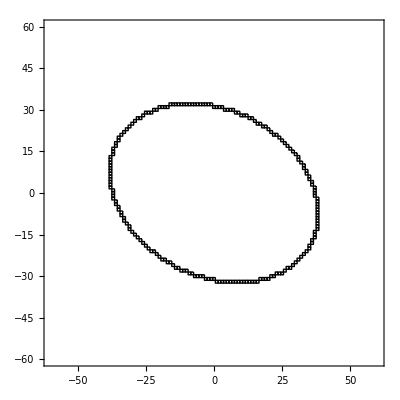

```mathematica
NestList[EllipseDiagonalIteration@@#&,ellipsefunction[{37,0},{-2,1},{40,30}],197];
Show[Graphics[unitsquare[First[#]]&/@%,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}]]
```

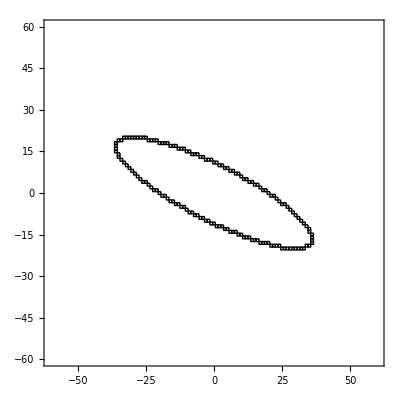

```mathematica
NestList[EllipseDiagonalIteration@@#&,ellipsefunction[{20,0},{-2,1},{40,10}],151];
Show[Graphics[unitsquare[First[#]]&/@%,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}]]
```

### Starting and stopping conditions

Finding a parametrization that will set the initial point onto an ellipse arc to be drawn, and that will tell the ellipse iteration program when to stop drawing, is not entirely straightforward. 
The most practical approach seems to be to define the initial and final tangent directions (because we happen to keep track of the partial derivatives of the discriminant Δ, anyway). Since every tangent direction occurs twice on the ellipse arc, we need to keep track of a direction, too, to resolve the ambiguity.

The tangent direction (t
u) is perpendicular to the gradient of the discriminant, i.e., 0=⟨t | u|(∂Δ)/(∂x) | (∂Δ)/(∂y)⟩=t(∂Δ)/(∂x)+u(∂Δ)/(∂y).

For the orientation of the direction, we require that initially, 0<⟨t | u|0 | 1
-1 | 0|(∂Δ)/(∂x) | (∂Δ)/(∂y)⟩=t(∂Δ)/(∂y)-u(∂Δ)/(∂x).

#### Stopping condition

Initially, the dot product ⟨t | u|(∂Δ)/(∂x) | (∂Δ)/(∂y)⟩ will go positive, i.e., the transition we are looking for as termination condition is a transition from negative to positive. 
If we want to be able to use the same tangent vector as starting and stopping condition, we must start testing for the stopping condition after the first iteration.

#### Starting condition

Problem:
Find the point on a discrete grid closest to the point that satisfies
0==A x^2+B y^2+2 C x y-D subject to 0==t(A x+C y)+u(C x+ B y) and 0<t(C x+ B y)-u(A x+C y).

Note the negaive sign, such that D>0, contrary to the definition further above.

```mathematica
FpPeS[FullSimplify[Solve[{0==A x^2+B y^2+2 C x y-D,0==t(A x+C y)+u(C x+B y)},{x,y}]]]
```

{{x→-(√D (C t+B u))/(√(A B-C^2) √(A t^2+u (2 C t+B u))),y→(√D (A t+C u))/(√(A B-C^2) √(A t^2+u (2 C t+B u)))},{x→(√D (C t+B u))/(√(A B-C^2) √(A t^2+u (2 C t+B u))),y→-(√D (A t+C u))/(√(A B-C^2) √(A t^2+u (2 C t+B u)))}}

√(D/((A B-C^2)(A t^2+B u^2+2 C t u)))(±(C t+ B u)
∓(A t+C u))

```mathematica
{A->b^2 ξ^2+a^2 υ^2,B->a^2 ξ^2+b^2 υ^2,C->(-a^2+b^2) ξ υ,D->a^2 b^2 (ξ^2+υ^2)}
Simplify[√(D/((A B-C^2)(A t^2+B u^2+2 C t u)))/.%]
Simplify[{C t+B u,A t+C u}/.%%]
```

{A→b^2 ξ^2+a^2 υ^2,B→a^2 ξ^2+b^2 υ^2,C→(-a^2+b^2) ξ υ,D→a^2 b^2 (ξ^2+υ^2)}

√(1/((ξ^2+υ^2) (a^2 (u ξ-t υ)^2+b^2 (t ξ+u υ)^2)))

{a^2 ξ (u ξ-t υ)+b^2 υ (t ξ+u υ),a^2 υ (-u ξ+t υ)+b^2 ξ (t ξ+u υ)}

```mathematica
Collect[(a^2 (u ξ-t υ)^2+b^2 (t ξ+u υ)^2),{u,t}]
```

t u (-2 a^2 ξ υ+2 b^2 ξ υ)+t^2 (b^2 ξ^2+a^2 υ^2)+u^2 (a^2 ξ^2+b^2 υ^2)

```mathematica
{A->b^2 ξ^2+a^2 υ^2,B->a^2 ξ^2+b^2 υ^2,C->(-a^2+b^2) ξ υ,D->a^2 b^2 (ξ^2+υ^2)}
Simplify[√(D/(A B-C^2))/.%]
```

{A→b^2 ξ^2+a^2 υ^2,B→a^2 ξ^2+b^2 υ^2,C→(-a^2+b^2) ξ υ,D→a^2 b^2 (ξ^2+υ^2)}

√(1/(ξ^2+υ^2))

1/(√((ξ^2+υ^2)(A t^2+B u^2+2 C t u)))(±(C t+ B u)
∓(A t+C u))

### Numeric range considerations

We need to make sure that the quantities used in the computations do not overflow.

```mathematica
ellipsediscriminant
```

2 (-a^2+b^2) x y ξ υ-a^2 b^2 (ξ^2+υ^2)+x^2 (b^2 ξ^2+a^2 υ^2)+y^2 (a^2 ξ^2+b^2 υ^2)

```mathematica
ellipsematrixeqns={A==b^2 ξ^2+a^2 υ^2,B==a^2 ξ^2+b^2 υ^2,C==(-a^2+b^2) ξ υ,D==a^2 b^2 (ξ^2+υ^2)}
```

{A==b^2 ξ^2+a^2 υ^2,B==a^2 ξ^2+b^2 υ^2,C==(-a^2+b^2) ξ υ,D==a^2 b^2 (ξ^2+υ^2)}

```mathematica
Collect[D[ellipsediscriminant,#],{x,y},Simplify]&/@{x,y}
D[%,#]&/@{x,y}
```

{2 (-a^2+b^2) y ξ υ+2 x (b^2 ξ^2+a^2 υ^2),2 (-a^2+b^2) x ξ υ+2 y (a^2 ξ^2+b^2 υ^2)}

{{2 (b^2 ξ^2+a^2 υ^2),2 (-a^2+b^2) ξ υ},{2 (-a^2+b^2) ξ υ,2 (a^2 ξ^2+b^2 υ^2)}}

```mathematica
{C t+B u,A t+C u}/.LSolve[ellipsematrixeqns,{A,B,C,D}]
```

{-(a^2-b^2) t ξ υ+u (a^2 ξ^2+b^2 υ^2),-(a^2-b^2) u ξ υ+t (b^2 ξ^2+a^2 υ^2)}

```mathematica
A t^2+B u^2+2 C t u/.LSolve[ellipsematrixeqns,{A,B,C,D}]
```

-2 (a^2-b^2) t u ξ υ+t^2 (b^2 ξ^2+a^2 υ^2)+u^2 (a^2 ξ^2+b^2 υ^2)

In the final iterations, we must scale the matrix elements A, B, C, and D such that the iteration states can't overflow.

#### Using normalization to alleviate dynamic range and roundoff problems

To help restricting the numerical range of quantities, it helps to normalize the vectors describing the principal axis (ξ
υ) and the tangent direction (t
u) to unit magnitude.

```mathematica
ellipsematrixeqns/.{ξ^2+υ^2->1}
```

{A==b^2 ξ^2+a^2 υ^2,B==a^2 ξ^2+b^2 υ^2,C==(-a^2+b^2) ξ υ,D==a^2 b^2}

### Implementation of ellipse drawing with starting and stopping conditions

This version uses {x,Ξ,ab}, where
x is the 2–dimensional initial coordinate vector
Ξ is the 2–dimensional direction of the first principal axis
ab is the 2–dimensional vector of principal axis lengths

```mathematica
ellipsebegin=Function[{Τ,Ξ,ab},Block[{τ=Τ,ξ=Ξ,A,B,C,D,x,Δ,dΔ},A=ab⟦2⟧^2 ξ⟦1⟧^2+ab⟦1⟧^2 ξ⟦2⟧^2;B=ab⟦1⟧^2 ξ⟦1⟧^2+ab⟦2⟧^2 ξ⟦2⟧^2;C=(ab⟦2⟧^2-ab⟦1⟧^2) ξ⟦1⟧ ξ⟦2⟧;D=(ab⟦1⟧ ab⟦2⟧)^2(ξ.ξ);x=Round[({{0,1},{-1,0}}.{{A,C},{C,B}}.τ)/(√((ξ.ξ)(τ.{{A,C},{C,B}}.τ)))];{x,{Δ=A x⟦1⟧^2+B x⟦2⟧^2+2 C x⟦1⟧ x⟦2⟧-D,dΔ=2 {A x⟦1⟧+C x⟦2⟧,C x⟦1⟧+B x⟦2⟧}},{A,B,C}}]]
```

Function[{Τ,Ξ,ab},Block[{τ=Τ,ξ=Ξ,A,B,C,D,x,Δ,dΔ},A=ab⟦2⟧^2 ξ⟦1⟧^2+ab⟦1⟧^2 ξ⟦2⟧^2;B=ab⟦1⟧^2 ξ⟦1⟧^2+ab⟦2⟧^2 ξ⟦2⟧^2;C=(ab⟦2⟧^2-ab⟦1⟧^2) ξ⟦1⟧ ξ⟦2⟧;D=(ab⟦1⟧ ab⟦2⟧)^2 ξ.ξ;x=Round[({{0,1},{-1,0}}.{{A,C},{C,B}}.τ)/(√(ξ.ξ τ.{{A,C},{C,B}}.τ))];{x,{Δ=A x⟦1⟧^2+B x⟦2⟧^2+2 C x⟦1⟧ x⟦2⟧-D,dΔ=2 {A x⟦1⟧+C x⟦2⟧,C x⟦1⟧+B x⟦2⟧}},{A,B,C}}]]

This version iterates {x, iterationvariables, iterationconstants}, where
x is the 2–dimensional coordinate vector
iterationvariables≡{Δ,dΔ}, where
Δ is the discriminant
dΔ≡{(∂Δ)/(∂x),(∂Δ)/(∂y)}
iterationconstants are the matrix elements {A,B,C}

Now put everything together

```mathematica
EllipseDraw=Function[{τ1,τ2,Ξ,ab},
NestWhileList[EllipseDiagonalIteration@@#&,ellipsebegin[τ1,Ξ,ab],!((τ2.#1⟦2,2⟧<0)&&(τ2.#2⟦2,2⟧≥0))&,2]
]
```

Function[{τ1,τ2,Ξ,ab},NestWhileList[EllipseDiagonalIteration@@#1&,ellipsebegin[τ1,Ξ,ab],!(τ2.#1⟦2,2⟧<0&&τ2.#2⟦2,2⟧≥0)&,2]]

### Examples

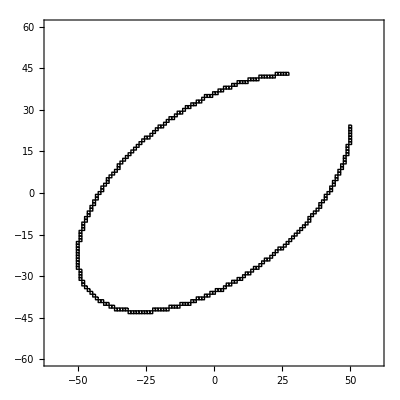

```mathematica
EllipseDraw[{-1,0},{0,1},{4,3},{58,31}];
Show[Graphics[unitsquare[First[#]]&/@%,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}]]
```

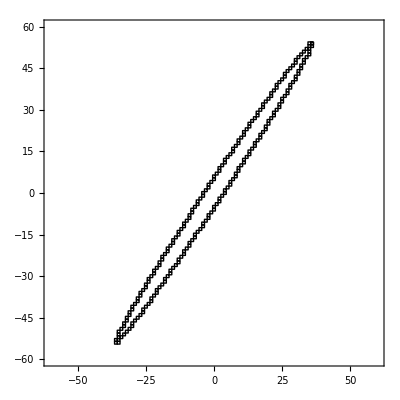

```mathematica
EllipseDraw[{-3,2},{-3,2},{2,3},{65,3}];
Show[Graphics[unitsquare[First[#]]&/@%,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}]]
```

### Verification

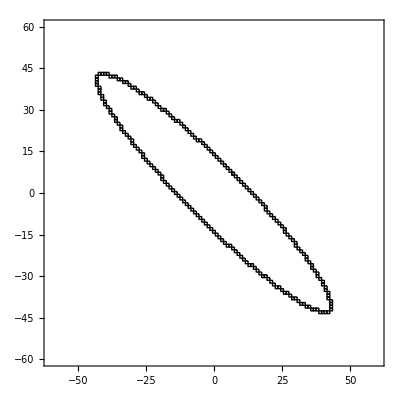

```mathematica
ell60=EllipseDraw@@{{-1,1},{-1,1},{1,-1},{60,10}};
Show[Graphics[unitsquare[First[#]]&/@ell60,Frame->True,AspectRatio->1,PlotRange->60{{-1,1},{-1,1}}]]
```

#### Data set of ellipse drawn

{{x,y},{Δ,{(∂Δ)/(∂x),(∂Δ)/(∂y)}},{A,B,C}}

```mathematica
ell60
```

{{{7,7},{-14400,{100800,100800}},{3700,3700,3500}},{{6,8},{-14000,{100400,101200}},{3700,3700,3500}},{{5,9},{-12800,{100000,101600}},{3700,3700,3500}},{{4,10},{-10800,{99600,102000}},{3700,3700,3500}},{{3,11},{-8000,{99200,102400}},{3700,3700,3500}},{{2,12},{-4400,{98800,102800}},{3700,3700,3500}},{{1,13},{0,{98400,103200}},{3700,3700,3500}},{{0,14},{5200,{98000,103600}},{3700,3700,3500}},{{-1,15},{11200,{97600,104000}},{3700,3700,3500}},{{-2,16},{18000,{97200,104400}},{3700,3700,3500}},{{-3,17},{25600,{96800,104800}},{3700,3700,3500}},{{-4,18},{34000,{96400,105200}},{3700,3700,3500}},{{-5,19},{43200,{96000,105600}},{3700,3700,3500}},{{-6,19},{-49100,{88600,98600}},{3700,3700,3500}},{{-7,20},{-38700,{88200,99000}},{3700,3700,3500}},{{-8,21},{-27500,{87800,99400}},{3700,3700,3500}},{{-9,22},{-15500,{87400,99800}},{3700,3700,3500}},{{-10,23},{-2700,{87000,100200}},{3700,3700,3500}},{{-11,24},{10900,{86600,100600}},{3700,3700,3500}},{{-12,25},{25300,{86200,101000}},{3700,3700,3500}},{{-13,26},{40500,{85800,101400}},{3700,3700,3500}},{{-14,26},{-41600,{78400,94400}},{3700,3700,3500}},{{-15,27},{-25200,{78000,94800}},{3700,3700,3500}},{{-16,28},{-8000,{77600,95200}},{3700,3700,3500}},{{-17,29},{10000,{77200,95600}},{3700,3700,3500}},{{-18,30},{28800,{76800,96000}},{3700,3700,3500}},{{-19,30},{-44300,{69400,89000}},{3700,3700,3500}},{{-20,31},{-24300,{69000,89400}},{3700,3700,3500}},{{-21,32},{-3500,{68600,89800}},{3700,3700,3500}},{{-22,33},{18100,{68200,90200}},{3700,3700,3500}},{{-23,34},{40500,{67800,90600}},{3700,3700,3500}},{{-24,34},{-23600,{60400,83600}},{3700,3700,3500}},{{-25,35},{0,{60000,84000}},{3700,3700,3500}},{{-26,36},{24400,{59600,84400}},{3700,3700,3500}},{{-27,36},{-31500,{52200,77400}},{3700,3700,3500}},{{-28,37},{-5900,{51800,77800}},{3700,3700,3500}},{{-29,38},{20500,{51400,78200}},{3700,3700,3500}},{{-30,38},{-27200,{44000,71200}},{3700,3700,3500}},{{-31,39},{400,{43600,71600}},{3700,3700,3500}},{{-32,40},{28800,{43200,72000}},{3700,3700,3500}},{{-33,40},{-10700,{35800,65000}},{3700,3700,3500}},{{-34,41},{18900,{35400,65400}},{3700,3700,3500}},{{-35,41},{-12800,{28000,58400}},{3700,3700,3500}},{{-36,42},{18000,{27600,58800}},{3700,3700,3500}},{{-37,42},{-5900,{20200,51800}},{3700,3700,3500}},{{-38,42},{-22400,{12800,44800}},{3700,3700,3500}},{{-39,43},{10000,{12400,45200}},{3700,3700,3500}},{{-40,43},{1300,{5000,38200}},{3700,3700,3500}},{{-41,43},{0,{-2400,31200}},{3700,3700,3500}},{{-42,43},{6100,{-9800,24200}},{3700,3700,3500}},{{-43,42},{6100,{-24200,9800}},{3700,3700,3500}},{{-43,41},{0,{-31200,2400}},{3700,3700,3500}},{{-43,40},{1300,{-38200,-5000}},{3700,3700,3500}},{{-43,39},{10000,{-45200,-12400}},{3700,3700,3500}},{{-42,38},{-22400,{-44800,-12800}},{3700,3700,3500}},{{-42,37},{-5900,{-51800,-20200}},{3700,3700,3500}},{{-42,36},{18000,{-58800,-27600}},{3700,3700,3500}},{{-41,35},{-12800,{-58400,-28000}},{3700,3700,3500}},{{-41,34},{18900,{-65400,-35400}},{3700,3700,3500}},{{-40,33},{-10700,{-65000,-35800}},{3700,3700,3500}},{{-40,32},{28800,{-72000,-43200}},{3700,3700,3500}},{{-39,31},{400,{-71600,-43600}},{3700,3700,3500}},{{-38,30},{-27200,{-71200,-44000}},{3700,3700,3500}},{{-38,29},{20500,{-78200,-51400}},{3700,3700,3500}},{{-37,28},{-5900,{-77800,-51800}},{3700,3700,3500}},{{-36,27},{-31500,{-77400,-52200}},{3700,3700,3500}},{{-36,26},{24400,{-84400,-59600}},{3700,3700,3500}},{{-35,25},{0,{-84000,-60000}},{3700,3700,3500}},{{-34,24},{-23600,{-83600,-60400}},{3700,3700,3500}},{{-34,23},{40500,{-90600,-67800}},{3700,3700,3500}},{{-33,22},{18100,{-90200,-68200}},{3700,3700,3500}},{{-32,21},{-3500,{-89800,-68600}},{3700,3700,3500}},{{-31,20},{-24300,{-89400,-69000}},{3700,3700,3500}},{{-30,19},{-44300,{-89000,-69400}},{3700,3700,3500}},{{-30,18},{28800,{-96000,-76800}},{3700,3700,3500}},{{-29,17},{10000,{-95600,-77200}},{3700,3700,3500}},{{-28,16},{-8000,{-95200,-77600}},{3700,3700,3500}},{{-27,15},{-25200,{-94800,-78000}},{3700,3700,3500}},{{-26,14},{-41600,{-94400,-78400}},{3700,3700,3500}},{{-26,13},{40500,{-101400,-85800}},{3700,3700,3500}},{{-25,12},{25300,{-101000,-86200}},{3700,3700,3500}},{{-24,11},{10900,{-100600,-86600}},{3700,3700,3500}},{{-23,10},{-2700,{-100200,-87000}},{3700,3700,3500}},{{-22,9},{-15500,{-99800,-87400}},{3700,3700,3500}},{{-21,8},{-27500,{-99400,-87800}},{3700,3700,3500}},{{-20,7},{-38700,{-99000,-88200}},{3700,3700,3500}},{{-19,6},{-49100,{-98600,-88600}},{3700,3700,3500}},{{-19,5},{43200,{-105600,-96000}},{3700,3700,3500}},{{-18,4},{34000,{-105200,-96400}},{3700,3700,3500}},{{-17,3},{25600,{-104800,-96800}},{3700,3700,3500}},{{-16,2},{18000,{-104400,-97200}},{3700,3700,3500}},{{-15,1},{11200,{-104000,-97600}},{3700,3700,3500}},{{-14,0},{5200,{-103600,-98000}},{3700,3700,3500}},{{-13,-1},{0,{-103200,-98400}},{3700,3700,3500}},{{-12,-2},{-4400,{-102800,-98800}},{3700,3700,3500}},{{-11,-3},{-8000,{-102400,-99200}},{3700,3700,3500}},{{-10,-4},{-10800,{-102000,-99600}},{3700,3700,3500}},{{-9,-5},{-12800,{-101600,-100000}},{3700,3700,3500}},{{-8,-6},{-14000,{-101200,-100400}},{3700,3700,3500}},{{-7,-7},{-14400,{-100800,-100800}},{3700,3700,3500}},{{-6,-8},{-14000,{-100400,-101200}},{3700,3700,3500}},{{-5,-9},{-12800,{-100000,-101600}},{3700,3700,3500}},{{-4,-10},{-10800,{-99600,-102000}},{3700,3700,3500}},{{-3,-11},{-8000,{-99200,-102400}},{3700,3700,3500}},{{-2,-12},{-4400,{-98800,-102800}},{3700,3700,3500}},{{-1,-13},{0,{-98400,-103200}},{3700,3700,3500}},{{0,-14},{5200,{-98000,-103600}},{3700,3700,3500}},{{1,-15},{11200,{-97600,-104000}},{3700,3700,3500}},{{2,-16},{18000,{-97200,-104400}},{3700,3700,3500}},{{3,-17},{25600,{-96800,-104800}},{3700,3700,3500}},{{4,-18},{34000,{-96400,-105200}},{3700,3700,3500}},{{5,-19},{43200,{-96000,-105600}},{3700,3700,3500}},{{6,-19},{-49100,{-88600,-98600}},{3700,3700,3500}},{{7,-20},{-38700,{-88200,-99000}},{3700,3700,3500}},{{8,-21},{-27500,{-87800,-99400}},{3700,3700,3500}},{{9,-22},{-15500,{-87400,-99800}},{3700,3700,3500}},{{10,-23},{-2700,{-87000,-100200}},{3700,3700,3500}},{{11,-24},{10900,{-86600,-100600}},{3700,3700,3500}},{{12,-25},{25300,{-86200,-101000}},{3700,3700,3500}},{{13,-26},{40500,{-85800,-101400}},{3700,3700,3500}},{{14,-26},{-41600,{-78400,-94400}},{3700,3700,3500}},{{15,-27},{-25200,{-78000,-94800}},{3700,3700,3500}},{{16,-28},{-8000,{-77600,-95200}},{3700,3700,3500}},{{17,-29},{10000,{-77200,-95600}},{3700,3700,3500}},{{18,-30},{28800,{-76800,-96000}},{3700,3700,3500}},{{19,-30},{-44300,{-69400,-89000}},{3700,3700,3500}},{{20,-31},{-24300,{-69000,-89400}},{3700,3700,3500}},{{21,-32},{-3500,{-68600,-89800}},{3700,3700,3500}},{{22,-33},{18100,{-68200,-90200}},{3700,3700,3500}},{{23,-34},{40500,{-67800,-90600}},{3700,3700,3500}},{{24,-34},{-23600,{-60400,-83600}},{3700,3700,3500}},{{25,-35},{0,{-60000,-84000}},{3700,3700,3500}},{{26,-36},{24400,{-59600,-84400}},{3700,3700,3500}},{{27,-36},{-31500,{-52200,-77400}},{3700,3700,3500}},{{28,-37},{-5900,{-51800,-77800}},{3700,3700,3500}},{{29,-38},{20500,{-51400,-78200}},{3700,3700,3500}},{{30,-38},{-27200,{-44000,-71200}},{3700,3700,3500}},{{31,-39},{400,{-43600,-71600}},{3700,3700,3500}},{{32,-40},{28800,{-43200,-72000}},{3700,3700,3500}},{{33,-40},{-10700,{-35800,-65000}},{3700,3700,3500}},{{34,-41},{18900,{-35400,-65400}},{3700,3700,3500}},{{35,-41},{-12800,{-28000,-58400}},{3700,3700,3500}},{{36,-42},{18000,{-27600,-58800}},{3700,3700,3500}},{{37,-42},{-5900,{-20200,-51800}},{3700,3700,3500}},{{38,-42},{-22400,{-12800,-44800}},{3700,3700,3500}},{{39,-43},{10000,{-12400,-45200}},{3700,3700,3500}},{{40,-43},{1300,{-5000,-38200}},{3700,3700,3500}},{{41,-43},{0,{2400,-31200}},{3700,3700,3500}},{{42,-43},{6100,{9800,-24200}},{3700,3700,3500}},{{43,-42},{6100,{24200,-9800}},{3700,3700,3500}},{{43,-41},{0,{31200,-2400}},{3700,3700,3500}},{{43,-40},{1300,{38200,5000}},{3700,3700,3500}},{{43,-39},{10000,{45200,12400}},{3700,3700,3500}},{{42,-38},{-22400,{44800,12800}},{3700,3700,3500}},{{42,-37},{-5900,{51800,20200}},{3700,3700,3500}},{{42,-36},{18000,{58800,27600}},{3700,3700,3500}},{{41,-35},{-12800,{58400,28000}},{3700,3700,3500}},{{41,-34},{18900,{65400,35400}},{3700,3700,3500}},{{40,-33},{-10700,{65000,35800}},{3700,3700,3500}},{{40,-32},{28800,{72000,43200}},{3700,3700,3500}},{{39,-31},{400,{71600,43600}},{3700,3700,3500}},{{38,-30},{-27200,{71200,44000}},{3700,3700,3500}},{{38,-29},{20500,{78200,51400}},{3700,3700,3500}},{{37,-28},{-5900,{77800,51800}},{3700,3700,3500}},{{36,-27},{-31500,{77400,52200}},{3700,3700,3500}},{{36,-26},{24400,{84400,59600}},{3700,3700,3500}},{{35,-25},{0,{84000,60000}},{3700,3700,3500}},{{34,-24},{-23600,{83600,60400}},{3700,3700,3500}},{{34,-23},{40500,{90600,67800}},{3700,3700,3500}},{{33,-22},{18100,{90200,68200}},{3700,3700,3500}},{{32,-21},{-3500,{89800,68600}},{3700,3700,3500}},{{31,-20},{-24300,{89400,69000}},{3700,3700,3500}},{{30,-19},{-44300,{89000,69400}},{3700,3700,3500}},{{30,-18},{28800,{96000,76800}},{3700,3700,3500}},{{29,-17},{10000,{95600,77200}},{3700,3700,3500}},{{28,-16},{-8000,{95200,77600}},{3700,3700,3500}},{{27,-15},{-25200,{94800,78000}},{3700,3700,3500}},{{26,-14},{-41600,{94400,78400}},{3700,3700,3500}},{{26,-13},{40500,{101400,85800}},{3700,3700,3500}},{{25,-12},{25300,{101000,86200}},{3700,3700,3500}},{{24,-11},{10900,{100600,86600}},{3700,3700,3500}},{{23,-10},{-2700,{100200,87000}},{3700,3700,3500}},{{22,-9},{-15500,{99800,87400}},{3700,3700,3500}},{{21,-8},{-27500,{99400,87800}},{3700,3700,3500}},{{20,-7},{-38700,{99000,88200}},{3700,3700,3500}},{{19,-6},{-49100,{98600,88600}},{3700,3700,3500}},{{19,-5},{43200,{105600,96000}},{3700,3700,3500}},{{18,-4},{34000,{105200,96400}},{3700,3700,3500}},{{17,-3},{25600,{104800,96800}},{3700,3700,3500}},{{16,-2},{18000,{104400,97200}},{3700,3700,3500}},{{15,-1},{11200,{104000,97600}},{3700,3700,3500}},{{14,0},{5200,{103600,98000}},{3700,3700,3500}},{{13,1},{0,{103200,98400}},{3700,3700,3500}},{{12,2},{-4400,{102800,98800}},{3700,3700,3500}},{{11,3},{-8000,{102400,99200}},{3700,3700,3500}},{{10,4},{-10800,{102000,99600}},{3700,3700,3500}},{{9,5},{-12800,{101600,100000}},{3700,3700,3500}},{{8,6},{-14000,{101200,100400}},{3700,3700,3500}},{{7,7},{-14400,{100800,100800}},{3700,3700,3500}}}

Verify that the iterated Δ and the Δ computed from the coordinates match:

```mathematica
ellipsediscriminant
disc60=ellipsediscriminant/.{ξ->1,υ->-1,a->60,b->10}
```

2 (-a^2+b^2) x y ξ υ-a^2 b^2 (ξ^2+υ^2)+x^2 (b^2 ξ^2+a^2 υ^2)+y^2 (a^2 ξ^2+b^2 υ^2)

-720000+3700 x^2+7000 x y+3700 y^2

{x,y}	{Δ_computed,Δ_iterated}

```mathematica
TableForm[{#⟦1⟧,{disc60/.{x->#⟦1,1⟧,y->#⟦1,2⟧},First[#⟦2⟧]}}&/@ell60,TableDepth->2]
```

{7,7} | {-14400,-14400}
{6,8} | {-14000,-14000}
{5,9} | {-12800,-12800}
{4,10} | {-10800,-10800}
{3,11} | {-8000,-8000}
{2,12} | {-4400,-4400}
{1,13} | {0,0}
{0,14} | {5200,5200}
{-1,15} | {11200,11200}
{-2,16} | {18000,18000}
{-3,17} | {25600,25600}
{-4,18} | {34000,34000}
{-5,19} | {43200,43200}
{-6,19} | {-49100,-49100}
{-7,20} | {-38700,-38700}
{-8,21} | {-27500,-27500}
{-9,22} | {-15500,-15500}
{-10,23} | {-2700,-2700}
{-11,24} | {10900,10900}
{-12,25} | {25300,25300}
{-13,26} | {40500,40500}
{-14,26} | {-41600,-41600}
{-15,27} | {-25200,-25200}
{-16,28} | {-8000,-8000}
{-17,29} | {10000,10000}
{-18,30} | {28800,28800}
{-19,30} | {-44300,-44300}
{-20,31} | {-24300,-24300}
{-21,32} | {-3500,-3500}
{-22,33} | {18100,18100}
{-23,34} | {40500,40500}
{-24,34} | {-23600,-23600}
{-25,35} | {0,0}
{-26,36} | {24400,24400}
{-27,36} | {-31500,-31500}
{-28,37} | {-5900,-5900}
{-29,38} | {20500,20500}
{-30,38} | {-27200,-27200}
{-31,39} | {400,400}
{-32,40} | {28800,28800}
{-33,40} | {-10700,-10700}
{-34,41} | {18900,18900}
{-35,41} | {-12800,-12800}
{-36,42} | {18000,18000}
{-37,42} | {-5900,-5900}
{-38,42} | {-22400,-22400}
{-39,43} | {10000,10000}
{-40,43} | {1300,1300}
{-41,43} | {0,0}
{-42,43} | {6100,6100}
{-43,42} | {6100,6100}
{-43,41} | {0,0}
{-43,40} | {1300,1300}
{-43,39} | {10000,10000}
{-42,38} | {-22400,-22400}
{-42,37} | {-5900,-5900}
{-42,36} | {18000,18000}
{-41,35} | {-12800,-12800}
{-41,34} | {18900,18900}
{-40,33} | {-10700,-10700}
{-40,32} | {28800,28800}
{-39,31} | {400,400}
{-38,30} | {-27200,-27200}
{-38,29} | {20500,20500}
{-37,28} | {-5900,-5900}
{-36,27} | {-31500,-31500}
{-36,26} | {24400,24400}
{-35,25} | {0,0}
{-34,24} | {-23600,-23600}
{-34,23} | {40500,40500}
{-33,22} | {18100,18100}
{-32,21} | {-3500,-3500}
{-31,20} | {-24300,-24300}
{-30,19} | {-44300,-44300}
{-30,18} | {28800,28800}
{-29,17} | {10000,10000}
{-28,16} | {-8000,-8000}
{-27,15} | {-25200,-25200}
{-26,14} | {-41600,-41600}
{-26,13} | {40500,40500}
{-25,12} | {25300,25300}
{-24,11} | {10900,10900}
{-23,10} | {-2700,-2700}
{-22,9} | {-15500,-15500}
{-21,8} | {-27500,-27500}
{-20,7} | {-38700,-38700}
{-19,6} | {-49100,-49100}
{-19,5} | {43200,43200}
{-18,4} | {34000,34000}
{-17,3} | {25600,25600}
{-16,2} | {18000,18000}
{-15,1} | {11200,11200}
{-14,0} | {5200,5200}
{-13,-1} | {0,0}
{-12,-2} | {-4400,-4400}
{-11,-3} | {-8000,-8000}
{-10,-4} | {-10800,-10800}
{-9,-5} | {-12800,-12800}
{-8,-6} | {-14000,-14000}
{-7,-7} | {-14400,-14400}
{-6,-8} | {-14000,-14000}
{-5,-9} | {-12800,-12800}
{-4,-10} | {-10800,-10800}
{-3,-11} | {-8000,-8000}
{-2,-12} | {-4400,-4400}
{-1,-13} | {0,0}
{0,-14} | {5200,5200}
{1,-15} | {11200,11200}
{2,-16} | {18000,18000}
{3,-17} | {25600,25600}
{4,-18} | {34000,34000}
{5,-19} | {43200,43200}
{6,-19} | {-49100,-49100}
{7,-20} | {-38700,-38700}
{8,-21} | {-27500,-27500}
{9,-22} | {-15500,-15500}
{10,-23} | {-2700,-2700}
{11,-24} | {10900,10900}
{12,-25} | {25300,25300}
{13,-26} | {40500,40500}
{14,-26} | {-41600,-41600}
{15,-27} | {-25200,-25200}
{16,-28} | {-8000,-8000}
{17,-29} | {10000,10000}
{18,-30} | {28800,28800}
{19,-30} | {-44300,-44300}
{20,-31} | {-24300,-24300}
{21,-32} | {-3500,-3500}
{22,-33} | {18100,18100}
{23,-34} | {40500,40500}
{24,-34} | {-23600,-23600}
{25,-35} | {0,0}
{26,-36} | {24400,24400}
{27,-36} | {-31500,-31500}
{28,-37} | {-5900,-5900}
{29,-38} | {20500,20500}
{30,-38} | {-27200,-27200}
{31,-39} | {400,400}
{32,-40} | {28800,28800}
{33,-40} | {-10700,-10700}
{34,-41} | {18900,18900}
{35,-41} | {-12800,-12800}
{36,-42} | {18000,18000}
{37,-42} | {-5900,-5900}
{38,-42} | {-22400,-22400}
{39,-43} | {10000,10000}
{40,-43} | {1300,1300}
{41,-43} | {0,0}
{42,-43} | {6100,6100}
{43,-42} | {6100,6100}
{43,-41} | {0,0}
{43,-40} | {1300,1300}
{43,-39} | {10000,10000}
{42,-38} | {-22400,-22400}
{42,-37} | {-5900,-5900}
{42,-36} | {18000,18000}
{41,-35} | {-12800,-12800}
{41,-34} | {18900,18900}
{40,-33} | {-10700,-10700}
{40,-32} | {28800,28800}
{39,-31} | {400,400}
{38,-30} | {-27200,-27200}
{38,-29} | {20500,20500}
{37,-28} | {-5900,-5900}
{36,-27} | {-31500,-31500}
{36,-26} | {24400,24400}
{35,-25} | {0,0}
{34,-24} | {-23600,-23600}
{34,-23} | {40500,40500}
{33,-22} | {18100,18100}
{32,-21} | {-3500,-3500}
{31,-20} | {-24300,-24300}
{30,-19} | {-44300,-44300}
{30,-18} | {28800,28800}
{29,-17} | {10000,10000}
{28,-16} | {-8000,-8000}
{27,-15} | {-25200,-25200}
{26,-14} | {-41600,-41600}
{26,-13} | {40500,40500}
{25,-12} | {25300,25300}
{24,-11} | {10900,10900}
{23,-10} | {-2700,-2700}
{22,-9} | {-15500,-15500}
{21,-8} | {-27500,-27500}
{20,-7} | {-38700,-38700}
{19,-6} | {-49100,-49100}
{19,-5} | {43200,43200}
{18,-4} | {34000,34000}
{17,-3} | {25600,25600}
{16,-2} | {18000,18000}
{15,-1} | {11200,11200}
{14,0} | {5200,5200}
{13,1} | {0,0}
{12,2} | {-4400,-4400}
{11,3} | {-8000,-8000}
{10,4} | {-10800,-10800}
{9,5} | {-12800,-12800}
{8,6} | {-14000,-14000}
{7,7} | {-14400,-14400}

## Generalization to muralizer

### Numeric values for coordinates

To test the algorithm, define numeric coordinates for the suspension points and for the ends of the line to be drawn

```mathematica
SuspensionPoints={{-100,0},{100,0}}100
```

{{-10000,0},{10000,0}}

```mathematica
LineEnds={{-70,-120},{80,-20}}100
```

{{-7000,-12000},{8000,-2000}}

Range of random coordinates

```mathematica
RandomRange={{-100,100},{-200,0}}100
```

{{-10000,10000},{-20000,0}}

Range of plot coordinates

```mathematica
RPlotRange={{0,300},{0,300}}100
```

{{0,30000},{0,30000}}

Maximum number of iterations, to prevent runaway iterations if the termination condition is not met

```mathematica
MaximumIterations=300 100
```

30000

### Basic equation

To draw a straight line, the muralizer spoolers need to follow a trajectory defined by (r^2 | s^2)·(A | C
C | B)·(r^2
s^2)+(r^2 | s^2)·(D
E)+F==0, where r and s are the lengths of thread spooled.

### Iterated variables

The discriminant and its gradient need not be computed from scratch for each new point, but can be iterated, exploiting the fact that for continuous lines, each of the coordinate can only change by 0 or ±1.

#### Discriminant

```mathematica
a x^2+c x y+b y^2+d x+e y+f/.{x->r^2,y->s^2}
TableForm[%/.{{r->r+1},{r->r+1,s->s+1},{s->s+1},{r->r-1,s->s+1},{r->r-1},{r->r-1,s->s-1},{s->s-1},{r->r+1,s->s-1}}]
TableForm[Collect[#,{a,b,c,d,e,f},FullSimplify]&/@(%-%%)]
TableForm[FullSimplify[ListConvolve[{1,-1},%,1]]]
TableForm[Simplify[{-1,1,-1}.%%⟦#⟧]&/@{{1,2,3},{3,4,5},{5,6,7},{7,8,1}}]
```

f+d r^2+a r^4+e s^2+c r^2 s^2+b s^4

f+d (1+r)^2+a (1+r)^4+e s^2+c (1+r)^2 s^2+b s^4
f+d (1+r)^2+a (1+r)^4+e (1+s)^2+c (1+r)^2 (1+s)^2+b (1+s)^4
f+d r^2+a r^4+e (1+s)^2+c r^2 (1+s)^2+b (1+s)^4
f+d (-1+r)^2+a (-1+r)^4+e (1+s)^2+c (-1+r)^2 (1+s)^2+b (1+s)^4
f+d (-1+r)^2+a (-1+r)^4+e s^2+c (-1+r)^2 s^2+b s^4
f+d (-1+r)^2+a (-1+r)^4+e (-1+s)^2+c (-1+r)^2 (-1+s)^2+b (-1+s)^4
f+d r^2+a r^4+e (-1+s)^2+c r^2 (-1+s)^2+b (-1+s)^4
f+d (1+r)^2+a (1+r)^4+e (-1+s)^2+c (1+r)^2 (-1+s)^2+b (-1+s)^4

d (1+2 r)+a (-r^4+(1+r)^4)+c (1+2 r) s^2
d (1+2 r)+a (-r^4+(1+r)^4)+e (1+2 s)+c (1+r+s) (1+r+s+2 r s)+b (-s^4+(1+s)^4)
e (1+2 s)+c r^2 (1+2 s)+b (-s^4+(1+s)^4)
d (1-2 r)+a ((-1+r)^4-r^4)+e (1+2 s)+c (-1+r-s) (-1+r-s+2 r s)+b (-s^4+(1+s)^4)
d (1-2 r)+a ((-1+r)^4-r^4)+c (1-2 r) s^2
d (1-2 r)+a ((-1+r)^4-r^4)+e (1-2 s)+b ((-1+s)^4-s^4)-c (-1+r+s) (1-s+r (-1+2 s))
e (1-2 s)+c r^2 (1-2 s)+b ((-1+s)^4-s^4)
d (1+2 r)+a (-r^4+(1+r)^4)+e (1-2 s)+b ((-1+s)^4-s^4)-c (1+r-s) (-1+s+r (-1+2 s))

(-1+2 s) (e+c (1+r)^2+b (1+2 (-1+s) s))
(1+2 s) (e+c (1+r)^2+b (1+2 s (1+s)))
-(1+2 r) (d+a (1+2 r (1+r))+c (1+s)^2)
-(-1+2 r) (d+a (1+2 (-1+r) r)+c (1+s)^2)
-(1+2 s) (e+c (-1+r)^2+b (1+2 s (1+s)))
-(-1+2 s) (e+c (-1+r)^2+b (1+2 (-1+s) s))
(-1+2 r) (d+a (1+2 (-1+r) r)+c (-1+s)^2)
(1+2 r) (d+a (1+2 r (1+r))+c (-1+s)^2)

c (1+2 r) (1+2 s)
-c (-1+2 r) (1+2 s)
c (-1+2 r) (-1+2 s)
-c (1+2 r) (-1+2 s)

Step in r direction: a((r±1)^4-r^4)+(c s^2+d)((r±1)^2-r^2)
Step in s direction: b((s±1)^4-s^4)+(c r^2+e)((s±1)^2-s^2)
Diagonal step: sum of orthogonal steps, +c(r^2-(r±1)^2)(s^2-(s±1)^2)

#### Partial derivative of discriminant w.r.t. r^2

```mathematica
D[a x^2+c x y+b y^2+d x+e y+f,x]/.{x->r^2,y->s^2}
TableForm[%/.{{r->r+1},{r->r+1,s->s+1},{s->s+1},{r->r-1,s->s+1},{r->r-1},{r->r-1,s->s-1},{s->s-1},{r->r+1,s->s-1}}]
TableForm[Collect[#,{a,b,c,d,e,f},FullSimplify]&/@(%-%%)]
TableForm[FullSimplify[ListConvolve[{1,-1},%,1]]]
TableForm[Simplify[{-1,1,-1}.%%⟦#⟧]&/@{{1,2,3},{3,4,5},{5,6,7},{7,8,1}}]
```

d+2 a r^2+c s^2

d+2 a (1+r)^2+c s^2
d+2 a (1+r)^2+c (1+s)^2
d+2 a r^2+c (1+s)^2
d+2 a (-1+r)^2+c (1+s)^2
d+2 a (-1+r)^2+c s^2
d+2 a (-1+r)^2+c (-1+s)^2
d+2 a r^2+c (-1+s)^2
d+2 a (1+r)^2+c (-1+s)^2

a (2+4 r)
a (2+4 r)+c (1+2 s)
c (1+2 s)
a (2-4 r)+c (1+2 s)
a (2-4 r)
a (2-4 r)+c (1-2 s)
c (1-2 s)
a (2+4 r)+c (1-2 s)

c (-1+2 s)
c+2 c s
-2 a (1+2 r)
a (2-4 r)
-c (1+2 s)
c-2 c s
2 a (-1+2 r)
a (2+4 r)

0
0
0
0

#### Partial derivative of discriminant w.r.t. s^2

```mathematica
D[a x^2+c x y+b y^2+d x+e y+f,y]/.{x->r^2,y->s^2}
TableForm[%/.{{r->r+1},{r->r+1,s->s+1},{s->s+1},{r->r-1,s->s+1},{r->r-1},{r->r-1,s->s-1},{s->s-1},{r->r+1,s->s-1}}]
TableForm[Collect[#,{a,b,c,d,e,f},FullSimplify]&/@(%-%%)]
TableForm[FullSimplify[ListConvolve[{1,-1},%,1]]]
TableForm[Simplify[{-1,1,-1}.%%⟦#⟧]&/@{{1,2,3},{3,4,5},{5,6,7},{7,8,1}}]
```

e+c r^2+2 b s^2

e+c (1+r)^2+2 b s^2
e+c (1+r)^2+2 b (1+s)^2
e+c r^2+2 b (1+s)^2
e+c (-1+r)^2+2 b (1+s)^2
e+c (-1+r)^2+2 b s^2
e+c (-1+r)^2+2 b (-1+s)^2
e+c r^2+2 b (-1+s)^2
e+c (1+r)^2+2 b (-1+s)^2

c (1+2 r)
c (1+2 r)+b (2+4 s)
b (2+4 s)
c (1-2 r)+b (2+4 s)
c (1-2 r)
c (1-2 r)+b (2-4 s)
b (2-4 s)
c (1+2 r)+b (2-4 s)

2 b (-1+2 s)
b (2+4 s)
-c (1+2 r)
c-2 c r
-2 b (1+2 s)
b (2-4 s)
c (-1+2 r)
c+2 c r

0
0
0
0

#### Gradient of discriminant

```mathematica
(D[a x^2+c x y+b y^2+d x+e y+f,#]&/@{x,y})/.{x->r^2,y->s^2}
Outer[ReplaceAll,%,{{r->r+1},{r->r+1,s->s+1},{s->s+1},{r->r-1,s->s+1},{r->r-1},{r->r-1,s->s-1},{s->s-1},{r->r+1,s->s-1}},1];
TableForm[Transpose[%],TableDepth->1]
TableForm[Transpose[Map[Collect[#,{a,b,c,d,e,f},FullSimplify]&,%%-%%%,{2}]],TableDepth->1]
TableForm[Simplify[{-1,1,-1}.%⟦#⟧]&/@{{1,2,3},{3,4,5},{5,6,7},{7,8,1}},TableDepth->1]
```

{d+2 a r^2+c s^2,e+c r^2+2 b s^2}

{d+2 a (1+r)^2+c s^2,e+c (1+r)^2+2 b s^2}
{d+2 a (1+r)^2+c (1+s)^2,e+c (1+r)^2+2 b (1+s)^2}
{d+2 a r^2+c (1+s)^2,e+c r^2+2 b (1+s)^2}
{d+2 a (-1+r)^2+c (1+s)^2,e+c (-1+r)^2+2 b (1+s)^2}
{d+2 a (-1+r)^2+c s^2,e+c (-1+r)^2+2 b s^2}
{d+2 a (-1+r)^2+c (-1+s)^2,e+c (-1+r)^2+2 b (-1+s)^2}
{d+2 a r^2+c (-1+s)^2,e+c r^2+2 b (-1+s)^2}
{d+2 a (1+r)^2+c (-1+s)^2,e+c (1+r)^2+2 b (-1+s)^2}

{a (2+4 r),c (1+2 r)}
{a (2+4 r)+c (1+2 s),c (1+2 r)+b (2+4 s)}
{c (1+2 s),b (2+4 s)}
{a (2-4 r)+c (1+2 s),c (1-2 r)+b (2+4 s)}
{a (2-4 r),c (1-2 r)}
{a (2-4 r)+c (1-2 s),c (1-2 r)+b (2-4 s)}
{c (1-2 s),b (2-4 s)}
{a (2+4 r)+c (1-2 s),c (1+2 r)+b (2-4 s)}

{0,0}
{0,0}
{0,0}
{0,0}

Step in r direction: (±(4a((r±1)^3-r^3)+2(c s^2+d))
2c s((r±1)^2-r^2))
Step in s direction: (2c r((s∓1)^2-s^2)
∓(4b((s∓1)^3-s^3)+2(c r^2+e)))
Diagonal step: sum of orthogonal steps, +(±2c((s∓1)^2-s^2)
∓2c((r±1)^2-r^2))

#### Terms that need to be updated/recalculated per iteration

δr4≡(r±1)^4-r^4=δr4c±δr4d≡1+6 r^2±r(1+r^2)

```mathematica
Apart[(r+#)^4-r^4&/@{1,-1}]
Simplify[(#@@%)/2&/@{Plus,Subtract}]
```

{1+4 r+6 r^2+4 r^3,1-4 r+6 r^2-4 r^3}

{1+6 r^2,4 (r+r^3)}

δr3≡(r±1)^3-r^3=δr3c±δr3d≡3r±(1+3 r^2)

```mathematica
Apart[(r+#)^3-r^3&/@{1,-1}]
Simplify[(#@@%)/2&/@{Plus,Subtract}]
```

{1+3 r+3 r^2,-1+3 r-3 r^2}

{3 r,1+3 r^2}

### Setting up initial conditions for the iterations

```mathematica
coeffrules=FullSimplify[MapThread[Rule,{
{a,b,c,d,e,f},
{δx^2+δy^2,
δx^2+δy^2,
-2(δx^2+δy^2),
-2 (δx ΔX+δy ΔY)^2-4 (ΔX δy-δx ΔY) (δy (x-X0)-δx (y-Y0)),
-2 (δx ΔX+δy ΔY)^2+4 (ΔX δy-δx ΔY) (δy (x-X0)-δx (y-Y0)),
(ΔX^2+ΔY^2)((δx ΔX+δy ΔY)^2+4(δy (x-X0)-δx (y-Y0))^2)}}]/.{δx->x2-x1,δy->y2-y1,x->(x1+x2)/2,y->(y1+y2)/2,ΔX->Xb-Xa,ΔY->Yb-Ya,X0->(Xa+Xb)/2,Y0->(Ya+Yb)/2}]
```

{a→(x1-x2)^2+(y1-y2)^2,b→(x1-x2)^2+(y1-y2)^2,c→-2 ((x1-x2)^2+(y1-y2)^2),d→-2 ((x1-x2) (Xa-Xb)+(y1-y2) (Ya-Yb))^2+2 (-(Xa-Xb) (y1-y2)+(x1-x2) (Ya-Yb)) ((Xa+Xb) (y1-y2)+x1 (2 y2-Ya-Yb)+x2 (-2 y1+Ya+Yb)),e→-2 ((x1-x2) (Xa-Xb)+(y1-y2) (Ya-Yb))^2+2 ((Xa-Xb) (y1-y2)-(x1-x2) (Ya-Yb)) ((Xa+Xb) (y1-y2)+x1 (2 y2-Ya-Yb)+x2 (-2 y1+Ya+Yb)),f→((Xa-Xb)^2+(Ya-Yb)^2) (((x1-x2) (Xa-Xb)+(y1-y2) (Ya-Yb))^2+((Xa+Xb) (y1-y2)+x1 (2 y2-Ya-Yb)+x2 (-2 y1+Ya+Yb))^2)}

```mathematica
InitIteration[refpoints_]:=Function[{points},
Block[{
Xa=refpoints⟦1,1⟧,
Ya=refpoints⟦1,2⟧,
Xb=refpoints⟦2,1⟧,
Yb=refpoints⟦2,2⟧,
x1=points⟦1,1⟧,
y1=points⟦1,2⟧,
x2=points⟦2,1⟧,
y2=points⟦2,2⟧,
signum=If[#≥0,1,-1]&,
a,b,c,d,e,f,
finalPoint,
discriminant,
gradient,
sign
},
finalPoint=Round[{√((x2-Xa)^2+(y2-Ya)^2),√((x2-Xb)^2+(y2-Yb)^2)}];
{a,b,c,d,e,f}=({a,b,c,d,e,f}/.coeffrules);
discriminant=f+d r^2+a r^4+e s^2+c r^2 s^2+b s^4;
gradient=({d+2 a r^2+c s^2,e+c r^2+2 b s^2});
sign=signum[(x1-x2)(Xa-Xb)+(y1-y2)(Ya-Yb)];
{{r,s},{discriminant,gradient},{a,b,c,d,e,f,sign,finalPoint}}/.{r->Round[√((x1-Xa)^2+(y1-Ya)^2)],s->Round[√((x1-Xb)^2+(y1-Yb)^2)]}
]
]
```

```mathematica
InitIteration[SuspensionPoints][LineEnds]
```

{{12369,20809},{4831001909280000000000,{-450014508000000000,90014508000000000}},{325000000,325000000,-650000000,-268000000000000000,-92000000000000000,55360000000000000000000000,1,{18111,2828}}}

### Identifying quadrants and octants

Since r≥0 and s≥0, it doesn't make a difference if the sign of the derivatives of the discriminant w.r.t. {r,s} or  {x,y}≡{r^2,s^2} is computed.

### Diagonal iteration

Underlying general rules:
δx=-σ Sign[(∂Δ)/(∂y)], δy=σ Sign[(∂Δ)/(∂x)], with σ≡Sign[(x_1-x_2)(X_a-X_b)+(y_1-y_2)(Y_a-Y_b)]; the straight direction is the direction for which the change in Δ is smaller.

### "Cheating" iteration: compute discriminant and gradient from scratch each time

```mathematica
MuralizerIterationCheat=Function[{position,iterationvariables,iterationconstants},
Block[{r,s,
dfunc=Function[{r,s},f+d r^2+a r^4+e s^2+c r^2 s^2+b s^4],
dgradfunc=Function[{r,s},{d+2 a r^2+c s^2,e+c r^2+2 b s^2}],
a,b,c,d,e,f,sign,finalPoint,
signum=If[#≥0,1,-1]&,
σr,σs,
discriminant,
discriminantGradient,
orthogonalStep,
diagonalStep
},
{r,s}=position;
{a,b,c,d,e,f,sign,finalPoint}=iterationconstants;
discriminant=dfunc[r,s];
discriminantGradient=dgradfunc[r,s];
{σr,σs}=sign{{0,-1},{1,0}}.(signum/@discriminantGradient);
orthogonalStep=If[Abs[r discriminantGradient⟦1⟧]<Abs[s discriminantGradient⟦2⟧],
{σr,0},{0,σs}
];
diagonalStep={σr,σs};
Append[
If[Abs[dfunc@@(position+orthogonalStep)]<Abs[dfunc@@(position+diagonalStep)],
{position+orthogonalStep,{dfunc@@(position+orthogonalStep),dgradfunc@@(position+orthogonalStep)}},
{position+diagonalStep,{dfunc@@(position+diagonalStep),dgradfunc@@(position+diagonalStep)}}
],
iterationconstants]
]
]
```

Function[{position,iterationvariables,iterationconstants},Block[{r,s,dfunc=Function[{r,s},f+d r^2+a r^4+e s^2+c r^2 s^2+b s^4],dgradfunc=Function[{r,s},{d+2 a r^2+c s^2,e+c r^2+2 b s^2}],a,b,c,d,e,f,sign,finalPoint,signum=If[#1≥0,1,-1]&,σr,σs,discriminant,discriminantGradient,orthogonalStep,diagonalStep},{r,s}=position;{a,b,c,d,e,f,sign,finalPoint}=iterationconstants;discriminant=dfunc[r,s];discriminantGradient=dgradfunc[r,s];{σr,σs}=sign {{0,-1},{1,0}}.signum/@discriminantGradient;orthogonalStep=If[Abs[r discriminantGradient⟦1⟧]<Abs[s discriminantGradient⟦2⟧],{σr,0},{0,σs}];diagonalStep={σr,σs};Append[If[Abs[dfunc@@(position+orthogonalStep)]<Abs[dfunc@@(position+diagonalStep)],{position+orthogonalStep,{dfunc@@(position+orthogonalStep),dgradfunc@@(position+orthogonalStep)}},{position+diagonalStep,{dfunc@@(position+diagonalStep),dgradfunc@@(position+diagonalStep)}}],iterationconstants]]]

### Real iteration: Discriminant and gradients are iterated

```mathematica
MuralizerIteration=Function[{position,iterationvariables,iterationconstants},
Block[{r,s,
discriminant,
discriminantGradient,
a,b,c,d,e,f,sign,finalPoint,
signum=If[#≥0,1,-1]&,
σr,σs,
discriminantSteps,
gradientSteps,
gradients,
orthogonalStep,
diagonalStep,
discriminantValues
},
{r,s}=position;
{discriminant,discriminantGradient}=iterationvariables;
{a,b,c,d,e,f,sign,finalPoint}=iterationconstants;
{σr,σs}=sign{{0,-1},{1,0}}.(signum/@discriminantGradient);
discriminantSteps={
a(6 r^2+1+σr 4r(r^2+1))+(c s^2+d)(1+σr 2r),
b(6 s^2+1+σs 4s(s^2+1))+(c r^2+e)(1+σs 2s),
c(2r+σr)(2s+σs)
};
gradientSteps={
(1+σr 2 r){2a,c},
(1+σs 2s){c,2b}
};
orthogonalStep=(* {position step, discriminant step, discriminant gradient step} *)
If[Subtract@@Abs[discriminantGradient{r,s}]<0,
{{σr,0},{discriminantSteps⟦1⟧,gradientSteps⟦1⟧}},
{{0,σs},{discriminantSteps⟦2⟧,gradientSteps⟦2⟧}}];
diagonalStep={
{σr,σs},
{Plus@@discriminantSteps,Plus@@gradientSteps}};
discriminantValues=discriminant+{orthogonalStep⟦2,1⟧,diagonalStep⟦2,1⟧};
Append[{position,iterationvariables}+
If[Subtract@@Abs[discriminantValues]<0,
orthogonalStep,
diagonalStep
],
iterationconstants]
]
]
```

Function[{position,iterationvariables,iterationconstants},Block[{r,s,discriminant,discriminantGradient,a,b,c,d,e,f,sign,finalPoint,signum=If[#1≥0,1,-1]&,σr,σs,discriminantSteps,gradientSteps,gradients,orthogonalStep,diagonalStep,discriminantValues},{r,s}=position;{discriminant,discriminantGradient}=iterationvariables;{a,b,c,d,e,f,sign,finalPoint}=iterationconstants;{σr,σs}=sign {{0,-1},{1,0}}.signum/@discriminantGradient;discriminantSteps={a (6 r^2+1+σr 4 r (r^2+1))+(c s^2+d) (1+σr 2 r),b (6 s^2+1+σs 4 s (s^2+1))+(c r^2+e) (1+σs 2 s),c (2 r+σr) (2 s+σs)};gradientSteps={(1+σr 2 r) {2 a,c},(1+σs 2 s) {c,2 b}};orthogonalStep=If[Subtract@@Abs[discriminantGradient {r,s}]<0,{{σr,0},{discriminantSteps⟦1⟧,gradientSteps⟦1⟧}},{{0,σs},{discriminantSteps⟦2⟧,gradientSteps⟦2⟧}}];diagonalStep={{σr,σs},{Plus@@discriminantSteps,Plus@@gradientSteps}};discriminantValues=discriminant+{orthogonalStep⟦2,1⟧,diagonalStep⟦2,1⟧};Append[{position,iterationvariables}+If[Subtract@@Abs[discriminantValues]<0,orthogonalStep,diagonalStep],iterationconstants]]]

### Termination criterion

```mathematica
continueDrawing=Function[{position,iterationvariables,iterationconstants},
Block[{
gradient=iterationvariables⟦2⟧,
finalpoint=Last[iterationconstants],
distance
},
distance=(position-finalpoint).{{0,-1},{1,0}}.gradient;
2 distance^2>gradient.gradient
]
]
```

Function[{position,iterationvariables,iterationconstants},Block[{gradient=iterationvariables⟦2⟧,finalpoint=Last[iterationconstants],distance},distance=(position-finalpoint).{{0,-1},{1,0}}.gradient;2 distance^2>gradient.gradient]]

### testrun

#### Inverse transformation (to check results)

```mathematica
inversexform[refpoints_]:=Function[{radii},
Block[{ra=radii⟦1⟧,rb=radii⟦2⟧,xa=refpoints⟦1,1⟧,ya=refpoints⟦1,2⟧,xb=refpoints⟦2,1⟧,yb=refpoints⟦2,2⟧},
{(xa+xb)/2+((ra-rb) (ra+rb) (-xa+xb))/(2 ((-xa+xb)^2+(-ya+yb)^2))+((-ya+yb) √(-(-(ra-rb)^2+(-xa+xb)^2+(-ya+yb)^2) (-(ra+rb)^2+(-xa+xb)^2+(-ya+yb)^2)))/(2 ((-xa+xb)^2+(-ya+yb)^2)),(ya+yb)/2+((ra-rb) (ra+rb) (-ya+yb))/(2 ((-xa+xb)^2+(-ya+yb)^2))-((-xa+xb) √(-(-(ra-rb)^2+(-xa+xb)^2+(-ya+yb)^2) (-(ra+rb)^2+(-xa+xb)^2+(-ya+yb)^2)))/(2 ((-xa+xb)^2+(-ya+yb)^2))}
]
]
```

#### "cheat" transform

```mathematica
auxc=NestWhileList[MuralizerIterationCheat@@#&,InitIteration[SuspensionPoints][LineEnds],continueDrawing@@#&,1,MaximumIterations];
```

#### real transform

```mathematica
auxl=NestWhileList[MuralizerIteration@@#&,InitIteration[SuspensionPoints][LineEnds],continueDrawing@@#&,1,MaximumIterations];
```

#### Evaluation

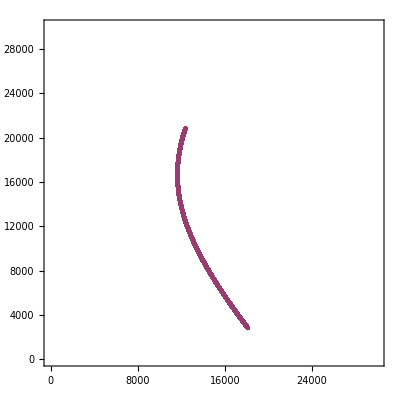

```mathematica
ListPlot[{First/@auxl,First/@auxc},Frame->True,PlotRange->RPlotRange,AspectRatio->1]
```

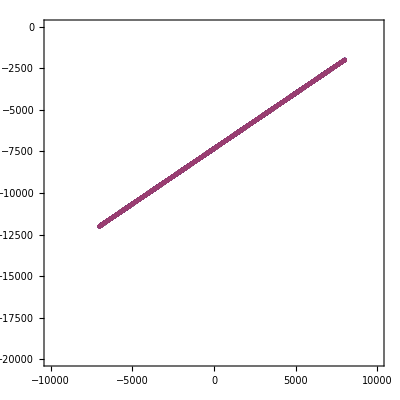

```mathematica
ListPlot[Map[inversexform[SuspensionPoints][First[#]]&,{auxl,auxc},{2}],Frame->True,PlotRange->RandomRange,AspectRatio->1]
```

```mathematica
Last[First[auxl]]
Last[First[auxc]]
```

{325000000,325000000,-650000000,-268000000000000000,-92000000000000000,55360000000000000000000000,1,{18111,2828}}

{325000000,325000000,-650000000,-268000000000000000,-92000000000000000,55360000000000000000000000,1,{18111,2828}}

```mathematica
Log[2.,Abs[Last[First[auxc]]]]
#-Max[#]&[%]
```

{28.2759,28.2759,29.2759,57.895,56.3525,85.517,0.,{14.1446,11.4656}}

{-57.2412,-57.2412,-56.2412,-27.622,-29.1646,0.,-85.517,{-71.3725,-74.0515}}

```mathematica
Log[2,$MachineEpsilon]
```

-52.

```mathematica
Dimensions/@{auxl,auxc}
```

{{17984,3},{17982,3}}

```mathematica
TableForm[auxc,TableDepth->1]
```

«1»

### several runs

```mathematica
coords=Table[{{Random[Real,RandomRange[[1]]],Random[Real,RandomRange[[2]]]},{Random[Real,RandomRange[[1]]],Random[Real,RandomRange[[2]]]}},{n,42}]
```

{{{1238.38,-8215.04},{-5341.97,-13644.8}},{{7764.11,-8424.56},{8147.45,-18779.4}},{{-4711.38,-4275.14},{-5407.34,-1698.1}},{{8941.99,-2946.62},{-4165.71,-9402.68}},{{-8380.25,-3534.53},{9004.19,-7107.78}},{{-6392.99,-5164.06},{9800.65,-3524.51}},{{2368.63,-16949.},{5142.62,-9879.71}},{{4604.51,-8524.46},{6995.17,-11100.3}},{{-684.11,-4249.32},{2402.52,-9402.23}},{{373.903,-1302.7},{-3431.77,-19999.6}},{{-1245.85,-17768.2},{-2435.96,-12891.8}},{{-4852.86,-12604.1},{-2236.61,-9367.26}},{{2778.52,-15655.1},{2620.77,-19487.5}},{{8174.,-7130.63},{5625.59,-8387.22}},{{-1141.89,-2881.31},{-6776.92,-18985.}},{{8484.21,-1578.62},{6654.84,-18985.4}},{{-269.944,-3810.45},{-909.2,-6093.67}},{{-5417.09,-11206.3},{-8672.59,-16726.4}},{{1804.39,-15551.3},{-1293.36,-17238.9}},{{3630.39,-8420.63},{3081.05,-8851.65}},{{-5227.72,-5539.32},{-142.03,-9866.66}},{{-3711.93,-3960.7},{3203.13,-10881.2}},{{6558.01,-150.251},{-5887.67,-4787.56}},{{1975.1,-8943.91},{-7215.08,-8061.15}},{{-9829.29,-13392.6},{4078.28,-10822.3}},{{-3459.68,-4972.02},{-9002.77,-1970.63}},{{-8231.96,-19432.7},{1139.26,-12104.}},{{5479.97,-15472.},{7936.14,-1222.74}},{{8921.96,-15321.7},{3823.81,-16435.2}},{{-3053.14,-6377.84},{1038.89,-8374.03}},{{-3223.85,-12985.2},{6960.61,-17551.7}},{{-9764.17,-8013.18},{5963.37,-15581.1}},{{8467.8,-8580.48},{-5175.89,-3477.15}},{{-7012.17,-13108.5},{-3112.03,-2254.42}},{{-5934.13,-17786.7},{3064.17,-5819.24}},{{7119.01,-11408.9},{-7974.72,-17445.2}},{{342.861,-18423.7},{-4935.33,-19893.5}},{{107.027,-10410.5},{-898.708,-4312.35}},{{1639.23,-1830.04},{-5722.82,-835.192}},{{-1348.59,-8721.57},{7389.21,-18580.8}},{{-5414.46,-10934.8},{-5674.96,-12761.5}},{{-2533.47,-19525.9},{-7700.23,-15316.3}}}

```mathematica
cheats=NestWhileList[MuralizerIterationCheat@@#&,InitIteration[SuspensionPoints][#],continueDrawing@@#&,1,MaximumIterations]&/@coords;
Dimensions/@cheats
```

{{8522,3},{10155,3},{1904,3},{13905,3},{16875,3},{15466,3},{7580,3},{3390,3},{5326,3},{14378,3},{4862,3},{4071,3},{3599,3},{2103,3},{13829,3},{17090,3},{1543,3},{6010,3},{3031,3},{678,3},{6636,3},{9679,3},{13149,3},{7497,3},{11601,3},{6009,3},{11646,3},{13720,3},{2911,3},{4426,3},{9762,3},{14487,3},{14418,3},{8174,3},{14827,3},{13282,3},{4076,3},{4440,3},{7425,3},{13165,3},{1619,3},{5418,3}}

```mathematica
curves=NestWhileList[MuralizerIteration@@#&,InitIteration[SuspensionPoints][#],continueDrawing@@#&,1,MaximumIterations]&/@coords;
Dimensions/@curves
```

{{8522,3},{10155,3},{1904,3},{13905,3},{16876,3},{15467,3},{7580,3},{3390,3},{5326,3},{14378,3},{4862,3},{4071,3},{3599,3},{2102,3},{13829,3},{17090,3},{1543,3},{6010,3},{3031,3},{678,3},{6636,3},{9679,3},{13149,3},{7497,3},{11602,3},{6010,3},{11646,3},{13721,3},{2911,3},{4426,3},{9762,3},{14487,3},{14419,3},{8174,3},{14827,3},{13282,3},{4076,3},{4440,3},{7426,3},{13165,3},{1619,3},{5418,3}}

#### "cheat" function

```mathematica
ListPlot[(First/@#)&/@cheats,Frame->True,PlotRange->RPlotRange,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[Map[inversexform[SuspensionPoints][First[#]]&,cheats,{2}],Frame->True,PlotRange->RandomRange,AspectRatio->1]
```

-Graphics-

#### function with iteration

```mathematica
ListPlot[(First/@#)&/@curves,Frame->True,PlotRange->RPlotRange,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[Map[inversexform[SuspensionPoints][First[#]]&,curves,{2}],Frame->True,PlotRange->RandomRange,AspectRatio->1]
```

-Graphics-